```mathematica
0.099*0.8
```

0.0792

```mathematica
Table[0,{i,2}]
```

{0,0}

```mathematica
{0.7,0.2,0.1}.markovChainMatrix
```

{0.66,0.24,0.1}

```mathematica
%.markovChainMatrix
```

{0.655556,0.244444,0.1}

```mathematica
markovChainMatrix[[1]]
```

{0.7,0.2,0.1}

```mathematica
markovChainMatrix[[3]].MatrixPower[markovChainMatrix,10]
```

{0.655556,0.244444,0.1}

```mathematica
%.markovChainMatrix
```

{0.655556,0.244444,0.1}

```mathematica
MatrixPower[markovChainMatrix,10]
```

{{0.655556,0.244444,0.1},{0.655556,0.244444,0.1},{0.655556,0.244444,0.1}}

```mathematica
markovChainMatrix[[1]].%
```

{0.655556,0.244444,0.1}

```mathematica
stateProb
```

{0.655556,0.244444,0.1}

```mathematica
Dimensions[wData]
```

{8759,27}

```mathematica
%[[1]]
```

8759

```mathematica
If[randomStateSequence[[1]]=="M", Print["yes"],Print["No"]]
```

yes

```mathematica
Length[availableResources]
```

2

```mathematica
For[i=1,i≤Length[availableResources],i++,
{availableResources[[i]] =  0.5*0.5*1.27*Pi*windSpeed[[10+i-1]]^3+1.2*100*solarRadi[[Mod[10+i-1,24]+1,month]]}
]
```

```mathematica
availableResources
```

{0,0}

```mathematica
availableResources
```

{2364.14,2295.29}

```mathematica
AvailableResource[100]
```

```mathematica
demand
```

{0,0}

```mathematica
Demand[100]
```

```mathematica
demand
```

{1042.13,1524.78}

```mathematica
x=3;
```

```mathematica
Minimize[2 x^2-3 x+5,x]
```

{31/8,{x→3/4}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Symbol x
```

Symbol x

```mathematica
?Symbol
```

Symbol[name] refers to a symbol with the specified name.

```mathematica
Symbol["x"]
```

3

```mathematica
x
```

3

```mathematica
markovChainMatrix//Grid
```

0.7 | 0.2 | 0.1
0.6 | 0.3 | 0.1
0.5 | 0.4 | 0.1

```mathematica
markovChainMatrix[[2,1]]
```

0.6

```mathematica
Demand[t]
```

```mathematica
demand
```

```mathematica
{227.92606784937996,2621.6552462433383}
```

{227.926,2621.66}

```mathematica
AvailableResource[3]
```

2227.78

```mathematica
Demand[10]
```

3244.87

```mathematica
randomStateSequence[[t]]=="N"
```

True

```mathematica
Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.5451903286421&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.1404817351918&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.418969944281&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.2864117800195&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.271050457528&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.2864117800195&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.120652501304&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.2864117800195},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]

```mathematica
Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]

```mathematica
Demand[t+1]
```

4992.16

```mathematica
RootApproximant[4992.155874107198]
```

1/3 (7483+√56152057)

```mathematica
xRB/.firstState
```

ReplaceAll::rmix: Elements of {219.78, {xGB → 0., xGC → 3311.72, xRB → 100., xRC → 2264.14, xRG → 0., xBC → 0., xBG → 0., yGB1 → 0., yGC1 → 0., yRB1 → 0., yRC1 → 408.838, yRG1 → 1886.45, yBC1 → 100., yBG1 → 0., yGB2 → 0., yGC2 → 315.457, yRB2 → 0., yRC2 → 2295.29, yRG2 → 0., yBC2 → 100., yBG2 → 0., yGB3 → 0., yGC3 → 3703.78, yRB3 → 0., yRC3 → 2295.29, yRG3 → 0., yBC3 → 100., yBG3 → 0.}} are a mixture of lists and nonlists.

xRB/.{219.78,{xGB→0.,xGC→3311.72,xRB→100.,xRC→2264.14,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→0.,yRB1→0.,yRC1→408.838,yRG1→1886.45,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→315.457,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→3703.78,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
t=101;
```

```mathematica
Minimize[{(xGB+xGC)*BuyPrice[t]+(initBatt+xGB+xRB-xBC-xBG)*ReserveCost[t] + (initBatt+xGB+xRB+xBC+xBG)*TransitionCost[t]-(xBG+xRG)*SellPrice[t]+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,1]],markovChainMatrix[[3,1]]]]*((yGB1+yGC1)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB1+yRB1-yBC1-yBG1)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB1+yRB1+yBC1+yBG1)*TransitionCost[t+1]-(yBG1+yRG1)*SellPrice[t])+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[2,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,2]],markovChainMatrix[3,2]]]*((yGB2+yGC2)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB2+yRB2-yBC2-yBG2)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB2+yRB2+yBC2+yBG2)*TransitionCost[t+1]-(yBG2+yRG2)*SellPrice[t+1])+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[3,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[3,2]],markovChainMatrix[[3,3]]]]*((yGB3+yGC3)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB3+yRB3-yBC3-yBG3)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB3+yRB3+yBC3+yBG3)*TransitionCost[t+1]-(yBG3+yRG3)*SellPrice[t+1]),xBC+xGC+xRC==Demand[t]&&
0≤ initBatt+xRB+xGB-xBG-xBC≤ capBat&&
xRG+xRB+xRC==AvailableResource[t]&&
xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&
yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&
yBC1+yGC1+yRC1==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB1+yGB1-yBG1-yBC1≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG1+yRB1+yRC1==AvailableResource[t+1]&&
yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&
yBC2+yGC2+yRC2==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB2+yGB2-yBG2-yBC2≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG2+yRB2+yRC2==AvailableResource[t+1]&&
yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&
yBC3+yGC3+yRC3==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB3+yGB3-yBG3-yBC3≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG3+yRB3+yRC3==AvailableResource[t+1]
},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-6745.67 + 1.\ xBC + 1.\ xGC ≤ 0, -4450.38 + 2.22045×10^-16\ xBC - xBG + xGB + 1.\ xGC - 1.\ xRG ≤ 0, 4450.38  - 1.\ xBC - 1.\ xGC + 1.\ xRG ≤ 0, « 11 », -2295.29 + 1.\ yRB3 + 1.\ yRG3 ≤ 0, 5595.27  - 2.22045×10^-16\ xBC + xBG - xGB - 1.\ xGC + 1.\ xRG + yBG3 - yGB3 - 1.\ yGC3 + 2.22045×10^-16\ yRB3 + 1.\ yRG3 ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMinimize::nnum: The function value -23.9126 - 15.5892\ {{0.7, 0.2, 0.1}, {0.6, 0.3, 0.1}, {0.5, 0.4, 0.1}}[3, 2] is not a number at {xBC, xBG, xGB, xGC, xRB, xRC, xRG, yBC1, yBC2, yBC3, yBG1, yBG2, yBG3, yGB1, yGB2, yGB3, yGC1, yGC2, yGC3, yRB1, yRB2, yRB3, yRC1, yRC2, yRC3, yRG1, yRG2, yRG3} = {0.00470214, 0.0480028, 0.0875684, 1.91742, -4448.46, 6743.75, 0.00383011, 6162.36, 2651.41, 1244.96, 0.00717069, 0.0602883, 0.0151694, « 2 », 1.99689, 0.0704125, 0.0776744, 0.0145263, 0.0671919, 0.0138445, 0.0767008, 2295.17, 2295.27, 2295.2, 0.0498376, 0.00506286, 0.00664789}.

```mathematica
Demand[t]
```

2766.42

```mathematica
RootApproximant[2766.423559567115]
```

1/3 (4154+√17183269)

```mathematica
initBatt=10
```

10

```mathematica
firstState
```

{181.643,{xGB→0.,xGC→1121.14,xRB→100.,xRC→2264.14,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→525.017,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→5772.76,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→956.673,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
secondStage
```

{595.931,{xGB→0.,xGC→4308.6,xRB→0.,xRC→2295.29,xRG→0.,xBC→4.54747×10^-13,xBG→0.,yGB1→0.,yGC1→6215.15,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→3645.38,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→1651.13,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
N[]0.5
```

0.5

```mathematica
secondStage
```

{150.822,{xGB→0.,xGC→2863.18,xRB→0.,xRC→2295.29,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→0.,yRB1→0.,yRC1→1059.04,yRG1→1236.25,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→1268.29,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→24.9867,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
initBatt=10;
```

```mathematica
Plot[StateMinimize[t,initBatt][[1]],{t, 1,100}]
```

Part::pspec: Part specification 1.00202 is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

-Graphics-

```mathematica
StateMinimize[10,initBatt][[1]]
```

-5889.05

```mathematica
For[i=1,i<1000,i++,(
StageMinimize
)]
```

```mathematica
Table[StageMinimize[t,initBatt][[1]],{t,1,10,1}]
```

{278.9,403.445,210.623,306.925,378.345,951.63,28.2298,-3132.68,-3687.57,-4722.19}

```mathematica
StageMinimize[6,0][[1]]
```

591.257

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

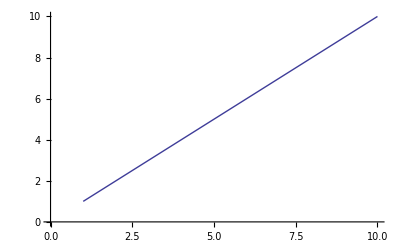

```mathematica
ListPlot[Range[10],Joined->True]
```

```mathematica
res ={}
```

{}

```mathematica
For[i=1,i<10,i++,(
res = Append[res,StageMinimize[i,initBatt][[1]]];
)]
```

NMinimize::argrx: NMinimize called with 3 arguments; 2 arguments are expected.

General::stop: Further output of NMinimize :: argrx will be suppressed during this calculation.

```mathematica
res
```

{524.626,603.697}

```mathematica
ListPlot[res,Joined->True]
```

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
Demand[t]
```

1331